### 2024/06/diffraction - 波的衍射 (20240602)

本文件提供对单缝衍射实验的模拟。函数 f[x,y,gap,phase]用于计算波长为 2π 的平行波通过中心位于(0,0)且宽度为 gap 的狭缝后，点(x,y)的振动情况。

```mathematica
f[x_,y_,gap_,phase_]:=NIntegrate[Sin[√(x^2+(y-t)^2)+phase]/gap,{t,-gap/2,gap/2}]
```

```mathematica
Plot3D[f[x,y,8,0],{x,0,16},{y,-18,18},ColorFunction->"TemperatureMap",Mesh->None,PlotPoints->15]
```

-Graphics3D-

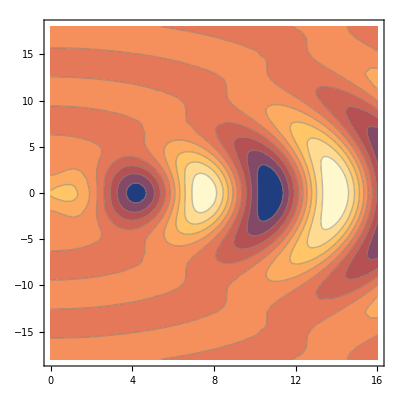

```mathematica
ContourPlot[f[x,y,8,0],{x,0,16},{y,-18,18},ContourStyle->Gray,PlotPoints->15]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"gap=2.gif"}],Table[Plot3D[f[x,y,2,phase],{x,0,16},{y,-18,18},ColorFunction->"TemperatureMap",Mesh->None,PlotPoints->15],{phase,2 π,0,-π/12}]]
Export[FileNameJoin[{NotebookDirectory[],"gap=8.gif"}],Table[Plot3D[f[x,y,8,phase],{x,0,16},{y,-18,18},ColorFunction->"TemperatureMap",Mesh->None,PlotPoints->15],{phase,2 π,0,-π/12}]]
Export[FileNameJoin[{NotebookDirectory[],"gap=2-8.gif"}],Table[Plot3D[f[x,y,gap,0],{x,0,16},{y,-18,18},ColorFunction->"TemperatureMap",Mesh->None,PlotPoints->15],{gap,1,8,0.5}]]
```